```mathematica
z=4;
γ[kx_,ky_]:=0.5*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,d_]:=2*Sqrt[(1+d^2+Sqrt[1+d^2]*γ[kx,ky])*(1-γ[kx,ky])];
bose[kx_,ky_,d_,T_]:=1/(Exp[ϵ[kx,ky,d]/T+0.00001]-1);
```

```mathematica
n=50;
d=0.5;
meanlength=Table[{T,2*π/(Sum[Sqrt[(2*π*i/n)^2+(2*π*j/n)^2]*bose[2*π*i/n,2*π*j/n,d,T],{i,0,n-1},{j,0,n-1}]/Sum[bose[2*π*i/n,2*π*j/n,d,T],{i,0,n-1},{j,0,n-1}])},{T,0.1,0.4,0.01}];
```

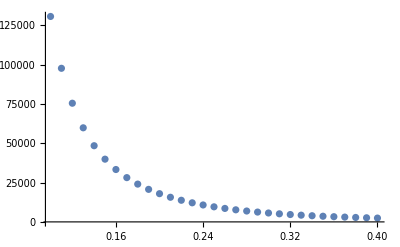

```mathematica
ListPlot[meanlength,PlotRange->All]
```

```mathematica
T=0.3;
d=0.1;
2*π/(Sum[Sqrt[(2*π*i/n)^2+(2*π*j/n)^2]*bose[2*π*i/n,2*π*j/n,d,T],{i,0,n-1},{j,0,n-1}]/Sum[bose[2*π*i/n,2*π*j/n,d,T],{i,0,n-1},{j,0,n-1}])
```

2875.64